```mathematica
data=Import["/home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p3.800_mu.100_0.nc","Data"]
```

Import::nffil: File /home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p3.800_mu.100_0.nc not found during Import.

$Failed

```mathematica
p0s=Flatten[Table[p,{p,3.85,3.9,0.01}]];
records={1,2,3,4,5,6,7,8,9};
```

```mathematica
timeEnergy=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p","_mu0.10_",".nc"},{p0s[[p]],records[[i]]},{3,0}],"Data"],{i,Length[records]}],{p,Length[p0s]}];
```

```mathematica
timeEnergy[[1,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
timeEnergyMean[[1,1]]
```

603.687

```mathematica
Table[Length[timeEnergy[[1,i,2]]],{i,Length[records]-1}]
```

{99,106,99,101,100,106,96,110}

```mathematica
Length[timeEnergyMean[[1]]]
```

110

```mathematica
time=Table[Table[Max[DeleteCases[Table[timeEnergy[[p,i,1,rec]],{i,Length[records]-1}],_Missing|_Part|0.]],{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}];
```

Part::partw: Part 97 of … does not exist.

Part::partw: Part 98 of … does not exist.

Part::partw: Part 99 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
timeEnergyMean=Table[Table[Mean[DeleteCases[Table[timeEnergy[[p,i,2,rec]],{i,Length[records]-1}],_Missing|_Part|0.]],{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}];
```

Part::partw: Part 97 of … does not exist.

Part::partw: Part 98 of … does not exist.

Part::partw: Part 99 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

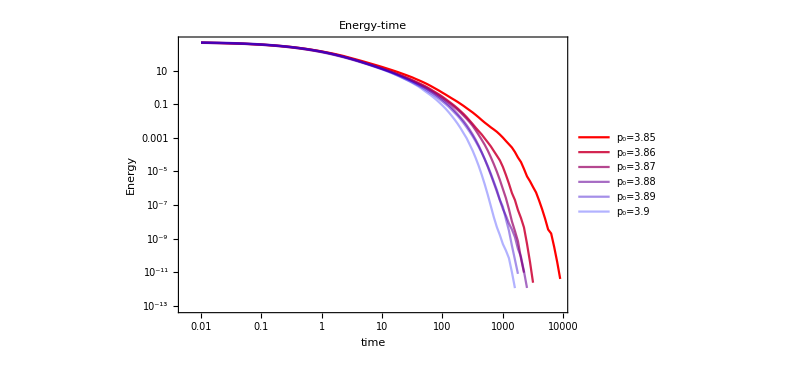

```mathematica
ListLogLogPlot[Table[Table[{time[[p,rec]],timeEnergyMean[[p,rec]]},{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"time","Energy"},ImageSize->600,PlotLabel->"Energy-time",Joined->True]
```

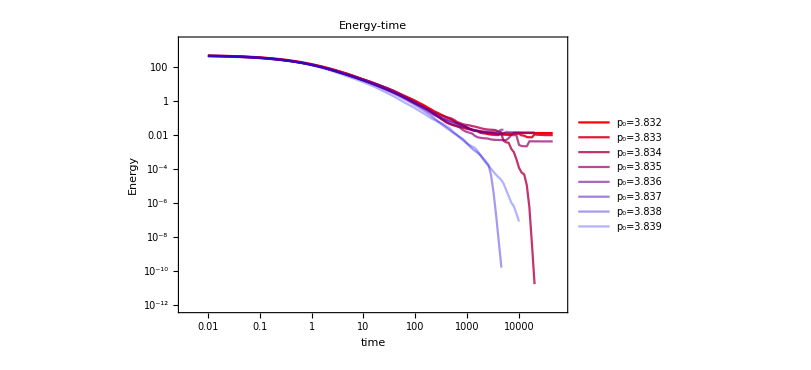

Part::partw: Part 118 of … does not exist.

Part::partw: Part 119 of … does not exist.

Part::partw: Part 120 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

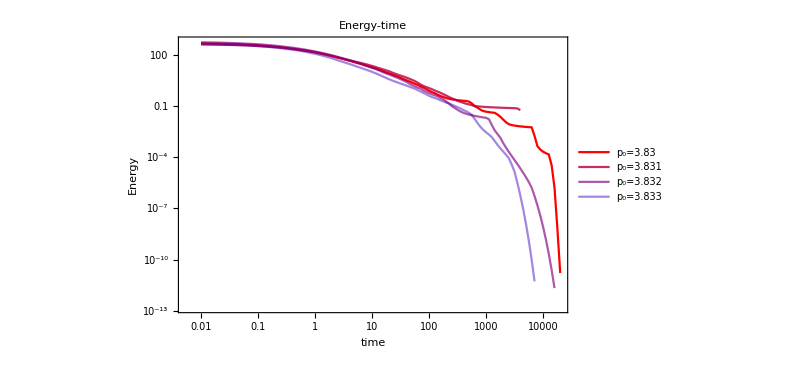

```mathematica
ListLogLogPlot[Table[Table[{timeEnergy[[14,i,1,rec]],timeEnergy[[15,i,2,rec]]},{rec,Length[timeEnergy[[14,1,1]]]}],{i,Length[records]-1}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,11,15}],PlotStyle->redBluePlotConfig[5],FrameLabel->{"time","Energy"},ImageSize->600,PlotLabel->"Energy-time",Joined->True]
```

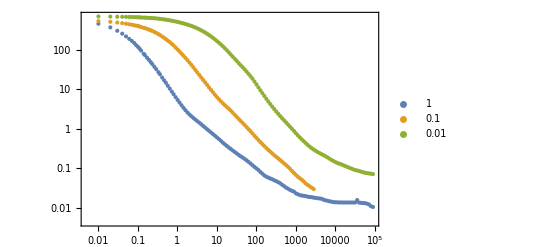

```mathematica
ListLogLogPlot[Table[Table[{timeEnergy[[mu,1,time]],timeEnergy[[mu,2,time]]},{time,Length[timeEnergy[[mu,1]]]}],{mu,3}],PlotLegends->{"1","0.1","0.01"}]
```

```mathematica
ListLogLogPlot[Table[Table[{timeEnergy[[mu,1,time]],timeEnergy[[mu,2,time]]},{time,Length[timeEnergy[[mu,1]]]}],{mu,3}],PlotLegends->{"1","0.1","0.01"}]
```

-Graphics-